```mathematica
f[x_]=x^2
fourier[x_]:=Sum[((-2/(Pi*I*k))-(2/((Pi*I*k)^2)))*(Cos[Pi*x*k]+I*Sin[Pi*x*k]),{k,-1,-1}]
```

x^2

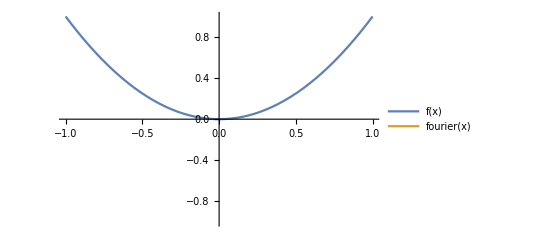

```mathematica
Plot[{f[x],fourier[x]},{x,-1,1},PlotRange->{-1,1},PlotLegends->"Expressions"]
```

Cos[2 x]

Cos[14 x]

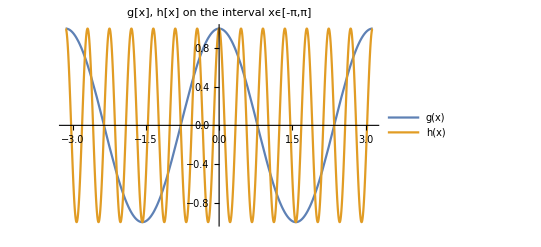

```mathematica
g[x_]=Cos[2*x]
h[x_]=Cos[14*x]
Plot[{g[x],h[x]},{x,-Pi,Pi},PlotRange->{-1,1},PlotLabel->"g[x], h[x] on the interval xϵ[-π,π]",PlotLegends->"Expressions"]
```

```mathematica
fhat[k_]=(-2/(Pi*I*k))-(2/((Pi*I*k)^2))
N[fhat[1]]
```

2/(k^2 π^2)+(2 ⅈ)/(k π)

0.202642+0.63662 ⅈ

```mathematica
N[fhat[-1]]
```

0.202642-0.63662 ⅈ

```mathematica
N[fhat[2]]
```

0.0506606+0.31831 ⅈ

```mathematica
N[fhat[-2]]
```

0.0506606-0.31831 ⅈ